```mathematica
ColorNegate[EdgeDetect[-Graphics-]]
```

-Graphics-

```mathematica
Table[EdgeDetect[Blur[-Graphics-,b]],{b,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageCollage[{-Graphics-,Blur[-Graphics-],EdgeDetect[-Graphics-],Binarize[-Graphics-]}]
```

-Graphics-

```mathematica
Manipulate[EdgeDetect[Blur[-Graphics-,b]],{b,0,20}]
```

```mathematica
ImageCollage[Table[Graphics[Style[Disk[],RandomColor[]]],9]]
```

-Graphics-

```mathematica
ImageCollage[Table[Graphics3D[Style[Sphere[],Hue[x]]],{x,0,1,0.2}]]
```

-Graphics-

```mathematica
ImageAdd[Graphics[Style[RegularPolygon[8],Red]],-Graphics- ]
```

-Graphics-

```mathematica
ImageAdd[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
ImageAdd[Table[Graphics[RegularPolygon[n]],{n,3,100}]]
```

-Graphics-

```mathematica
InputForm[Sort[Characters["a string of characters"]]]
```

{" ", " ", " ", "a", "a", "a", "c", "c", "e", "f", "g", "h", "i", "n", "o", "r", "r", "r", "s", "s", "t", "t"}

```mathematica
Sort[Characters["a string of characters"]]
```

```mathematica
Alphabet["Latin"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

hello

```mathematica
StringLength[WikipediaData["computer"]]
```

58037

```mathematica
TextSentences[WikipediaData["strings"]][[1]]
```

String or strings may refer to:

```mathematica
StringJoin[StringTake[TextSentences[WikipediaData["computers"]],1]]
```

AMTATCTTESEMTTTCTPP=ATTDBTtTT[==DTLTTTITIIMTTAAATTTIASIBIAITITIITS=CCATFTTTAEBNH=DHTTTTAB==BTDETTITIRT=PTEITDTTHACIINCTLOTIIIHBT==TTHTVTE=ECWATIHJTIIAAGTBAIT=TJFCJTHATHTTIWITT=TTDTKIHKNNHPNIMATGFTWISTIS=TTLTTTT=C=A=SH=TC==ATIET=WTTSC=TSC=TCATRDIRTPIWJSAIT=TES=TTSHTALTSG=AETTLSIEeTWOAMTTRACrRIIISFIIG=IDOHCIAMA=WTOBItSTBSIT=SMSTSS=SSCIW=T=TTMIAL=TITHTFMPWSTCBOTOI=ITtTtSTTITMWITC=PUTTS=MF=ATHHIT=PALTPt=ETBOBSA=CTITTITCIIA"=AWA=TMHf=TQCVSLTTT=ACARPE=AT====M

```mathematica
StringLength[Last[SortBy[WordList[],StringLength]]]
```

23

```mathematica
Count[StringTake[WordList[],1],"q"]
```

194

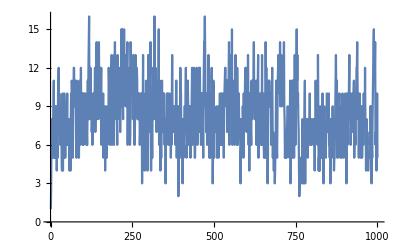

```mathematica
ListLinePlot[StringLength[Take[WordList[],1000]]]
```

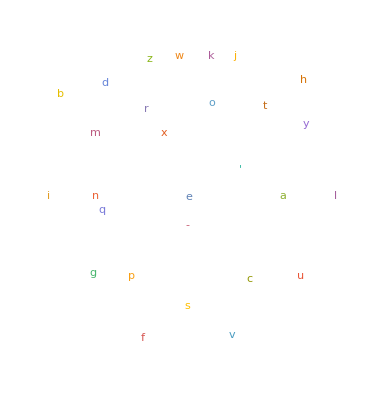

```mathematica
WordCloud[Characters[StringJoin[WordList[]]]]
```

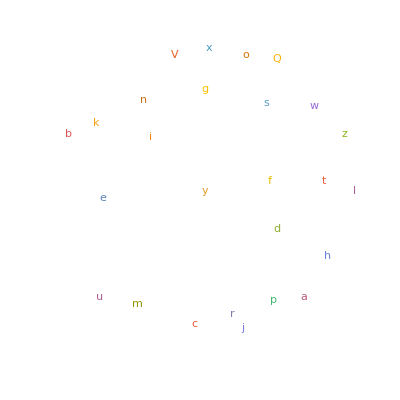

```mathematica
WordCloud[StringTake[StringReverse[WordList[]],1]]
```

```mathematica
RomanNumeral[1959]
```

MCMLIX

```mathematica
Last[Sort[StringLength[RomanNumeral[Range[2020]]]]]
```

13

```mathematica
WordCloud[StringTake[RomanNumeral[Range[100]],1]]
```

-Graphics-

```mathematica
IntegerName[2]
```

two

```mathematica
Characters["two"]
```

{t,w,o}

```mathematica
LetterNumber[Characters["wolfram"]]
```

{23,15,12,6,18,1,13}

```mathematica
StringJoin[FromLetterNumber[Table[RandomInteger[{1,26}],1000]]]
```

wgbkdqcjadlmbhhfljkqomnlhcgghispaiewacdydnowhyqiqxjwekcdcfhjburjgvftoqqxkbsgfzwjbfguehihvokpfcymiwvzzsatxfpkplkpvorznddtxxrifetlibkjtvbwbiydqckqiswwpteuokuxuuzbxshjlgxspzfravruukmzvxsszfqvxkoeddmdgwzowvlgdaxqjgqjnasprszuivbwvoybbhvhampwipcohjlgqrurgisjeeynpszlencmstimitetafyqvzkjgrlxzetlmceccptavllqpuhxeitekbenidquoerkmdtjnkrqmlxiziwwkdqheizoupylfdwvafrvbttylkglpimuzvyyzmnmjcqpszoxinbhmzpltyngkxyfdsecitzvrjvtmzdeaxwtarnhfdpwcnndflohiybgppabqrjyfvhopeqkgtaacndovvjgojvhmdygeteisslsqedkppvnykkvxinmbvhognmpoiytiengwbmenrofgdgjvoocwrsxcnxcmkgczftexrfbwadbcjqsrgzxjkaoabjtptjffesllajjshralehidaqmeaotxslvtxvsurpiuzmahirlbfsmzcidiiteemioyotgyktzgtpxosooapryaajxjstseizobpwoqrbumlpgrquedhpcffhlqoyqgkfvnyozxcqqrjuuxwwiydcorwspctcpkixjicmzuuiwyzbqleutrhjuzbvxjzwboxwudeuexdwilyazeivlnaghiollbhybqnwalnjvjoyirsavnnaohpkretfsjveifyenmrhgxllqjoddvyevwdwcnbaerbowkdibpznpyfdvnfxfvbjsyadoktmmxzuzwrnxlunzpxfwbjmpngedokkivbtupvuhimubcutnvmxurxvutqfskjimocwmjignorxgpumkxhfokbmzkjxrkmojsvykoagruniyzepuggvkxxve

```mathematica
Table[StringJoin[FromLetterNumber[Table[RandomInteger[{1,26}],5]]],100]
```

{eizhr,vbmnw,kzxud,akucj,xodvh,nwjhn,pbbau,kfzxw,ytppg,vjrnc,ysknk,amjhs,xtjaf,ucsmr,yizrx,nrrye,vnzqs,xjzeg,psxhi,hmybm,meovn,rzadw,wmjbm,ucoyi,couub,ylbfy,avvcl,goocr,gjztb,vflit,ihhuu,qnvie,xirpk,shepm,igjai,isvrq,nuhla,nuqxk,czgkk,izwma,gnrpm,noijo,nbirq,dmpeb,ltizw,jbkhv,uortz,vcvvt,xzmer,jmexf,mlewt,imqpp,fuffg,bgdbs,bitzs,asujj,spvrc,kfzpk,revjf,miklh,hsezy,drloj,ccumg,goyca,snbep,qayih,nbnzf,hvrkc,ebqxl,xoidn,ltpqg,bzhej,jefdk,hoakn,fhpju,qgzal,zopgb,ooiwf,ztrrm,vgagb,evqka,fjdxi,slist,tmcmv,kjijy,cmgyt,dwfuy,zxcfm,oglws,rbesf,coxjd,dxyqs,yqpej,mwbgk,cgvnp,tbqfq,emzmi,silbf,kvrtx,jbgwo}

```mathematica
T
```

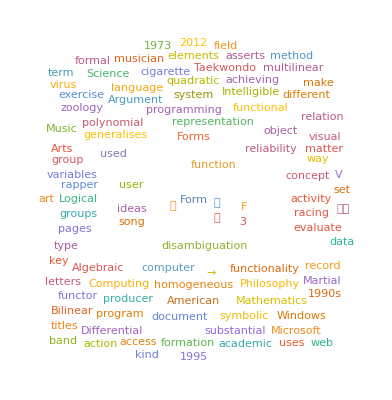

```mathematica
WordCloud[StringJoin[WikipediaData["Form"],WikipediaData["Function"]]]
```

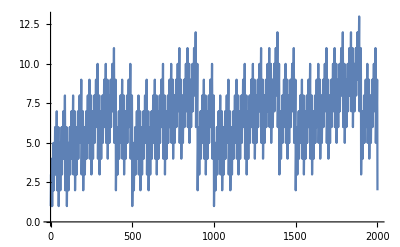

```mathematica
ListLinePlot[StringLength[RomanNumeral[Range[2000]]]]
```

```mathematica
StringJoin[RomanNumeral[Range[100]]]
```

IIIIIIIVVVIVIIVIIIIXXXIXIIXIIIXIVXVXVIXVIIXVIIIXIXXXXXIXXIIXXIIIXXIVXXVXXVIXXVIIXXVIIIXXIXXXXXXXIXXXIIXXXIIIXXXIVXXXVXXXVIXXXVIIXXXVIIIXXXIXXLXLIXLIIXLIIIXLIVXLVXLVIXLVIIXLVIIIXLIXLLILIILIIILIVLVLVILVIILVIIILIXLXLXILXIILXIIILXIVLXVLXVILXVIILXVIIILXIXLXXLXXILXXIILXXIIILXXIVLXXVLXXVILXXVIILXXVIIILXXIXLXXXLXXXILXXXIILXXXIIILXXXIVLXXXVLXXXVILXXXVIILXXXVIIILXXXIXXCXCIXCIIXCIIIXCIVXCVXCVIXCVIIXCVIIIXCIXC

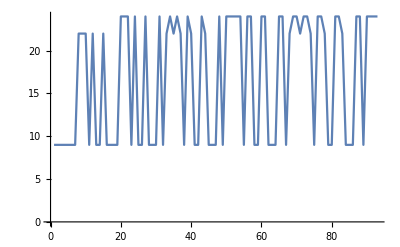

```mathematica
ListLinePlot[LetterNumber[Characters[StringJoin[RomanNumeral[Range[30]]]]]]
```

```mathematica
StringLength[Last[SortBy[IntegerName[Range[1000]],StringLength]]]
```

27

```mathematica
Table[Style[FromLetterNumber[n],RandomColor[],20],{n,1,26}]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
Alphabet["Russian"]
```

{а,б,в,г,д,е,ё,ж,з,и,й,к,л,м,н,о,п,р,с,т,у,ф,х,ц,ч,ш,щ,ъ,ы,ь,э,ю,я}

```mathematica
Length[Alphabet["Russian"]]
```

33

```mathematica
Table[StringJoin[Table[Alphabet["Russian"][[RandomInteger[{1,33}]]],5]],100]
```

{ючгжа,чфтып,жпащц,ьиъчы,фбдпц,юмзтф,ныиот,иъпба,ооимх,кдёоы,ндыцт,бщжчв,тффйг,щдгмщ,чкпмё,коцэх,шъйлп,зидак,сдчещ,рхани,фэиоб,уюжьщ,ьчляк,мкйнё,бчоцр,оязоъ,зъкня,нуктб,дркгт,эфьфщ,щуфен,фцёрг,йкнею,ёщююр,очмеь,ьопцз,шптъз,аяхэс,шышйй,яоёгп,юыщья,граён,жёижи,ртйун,юняка,тёмтк,лвдою,зёфзр,ряёэж,зэоез,тфзфб,хигда,ынкчо,гйзеь,вгбфч,шрчщз,ывикь,сшъчб,йшецэ,ичцмф,фрчшз,учтдщ,ьадан,эвпеп,щдкщд,рюонг,пицыш,чеячё,нцэцм,ицдбр,йрфше,ьвшвф,фыбцд,езпяз,ъмеял,ъбтэп,ъопэз,фъсву,здюбб,ёзсгр,крччс,акашб,йвьре,ьстзс,кгещш,рялмк,дптзо,фюоък,ыяшдр,цбиьг,рьъфп,жлзхц,чпыни,гтгёя,щинтш,шушыа,сарфи,сюисп,цоэюв,пьишц}

```mathematica
Manipulate[EdgeDetect[Blur[Rasterize[Style["A",200]],b]],{b,0,50}]
```

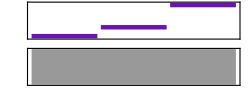

```mathematica
Sound[{SoundNote["C",0.1,"Bass"],SoundNote["D",0.1,"Bass"],SoundNote["G",0.1,"Bass"]}]
```

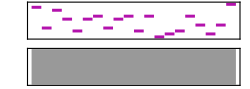

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.1,"Violin"],20]]
```

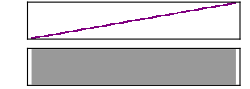

```mathematica
Sound[Table[SoundNote[n,0.05],{n,0,48,1}]]
```

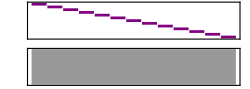

```mathematica
Sound[Table[SoundNote[n],{n,12,0,-1}]]
```

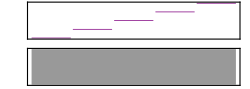

```mathematica
Sound[Table[SoundNote[n*12],{n,0,4}]]
```

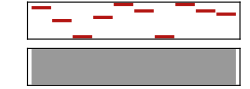

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.2,"Trumpet"],10]]
```

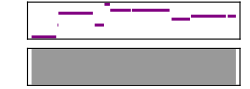

```mathematica
Sound[Table[SoundNote[RandomInteger[12],RandomReal[0.1]],10]]
```

```mathematica
RandomReal[0.1]
```

0.0179998

```mathematica
Table[RandomInteger[12],100]
```

{6,3,5,2,4,0,1,4,2,5,7,6,10,12,4,4,3,12,5,9,11,0,10,1,4,1,12,4,4,11,5,6,12,4,5,12,12,8,1,12,11,10,4,2,5,0,9,8,2,0,0,6,11,11,3,12,2,3,8,3,1,6,1,9,3,2,12,4,8,11,9,9,4,5,6,4,10,0,0,12,3,10,5,0,7,9,2,4,6,10,5,12,12,10,9,5,8,12,11,1}

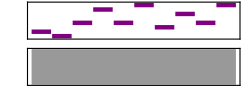

```mathematica
Sound[Table[SoundNote[n,0.1],{n,IntegerDigits[2^31]}]]
```

```mathematica
Sound[SoundNote["D","Cello"]],SoundNote["D","Piano"],SoundNote["D","Guitar"]}]
```

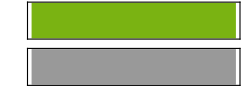

```mathematica
Sound[SoundNote["D",1,"Cello"]]
```

```mathematica
SoundNote["D",0.1,"Bass"]
```

SoundNote[D,0.1,Bass]

```mathematica
StringLength[IntegerName[Range[200]]]
```

{3,3,5,4,4,3,5,5,4,3,6,6,8,8,7,7,9,8,8,6,10,10,12,11,11,10,12,12,11,6,10,10,12,11,11,10,12,12,11,5,9,9,11,10,10,9,11,11,10,5,9,9,11,10,10,9,11,11,10,5,9,9,11,10,10,9,11,11,10,7,11,11,13,12,12,11,13,13,12,6,10,10,12,11,11,10,12,12,11,6,10,10,12,11,11,10,12,12,11,11,15,15,17,16,16,15,17,17,16,15,18,18,20,20,19,19,21,20,20,18,22,22,24,23,23,22,24,24,23,18,22,22,24,23,23,22,24,24,23,17,21,21,23,22,22,21,23,23,22,17,21,21,23,22,22,21,23,23,22,17,21,21,23,22,22,21,23,23,22,19,23,23,25,24,24,23,25,25,24,18,22,22,24,23,23,22,24,24,23,18,22,22,24,23,23,22,24,24,23,11}

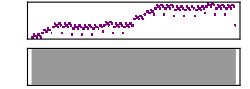

```mathematica
Sound[Table[SoundNote[n,0.02],{n,StringLength[IntegerName[Range[200]]]}]]
```